### Start choosing the example:

```mathematica
t=27;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{10,15}},Switching Costs→{}|>

```mathematica
Data["Entrance Vertices and Currents"]={{1,1}};
Data["Exit Vertices and Terminal Costs"]={{10,1000}};
```

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0&&j175-j186-u217+u228==0&&j176-j187-u218+u229==0&&j177-j188-u219+u230==0&&j178-j189-u220+u231==0&&j179-j190-u221+u232==0&&j180-j191-u222+u233==0&&j181-j192-u223+u234==0&&j182-j193-u224+u235==0&&j183-j194-u225+u236==0

EEX: -u217+u227==0.&&-1+u217-u218==0.&&-1+u218-u219==0.&&-1+u219-u220==0.&&-1+u220-u221==0.&&-1+u221-u222==0.&&-1+u222-u223==0.&&-1+u223-u224==0.&&-1+u224-u225==0.&&-1001+u225==0.

D2E: {True,<|j185→1,u237→1000,j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u226→1000,u228→-1+1009.,u229→-1+1008.,u230→-1+1007.,u231→-1+1006.,u232→-1+1005.,u233→-1+1004.,u234→-1+1003.,u235→-1+1002.,u236→-1+1001.,u238→1009.,u217→1009.,u218→1008.,u219→1007.,u220→1006.,u221→1005.,u222→1004.,u223→1003.,u224→1002.,u225→1001.,u227→1009.|>}

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.031181,Null}

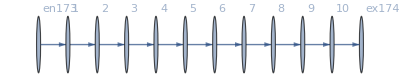

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1009.,u218→1008.,u219→1007.,u220→1006.,u221→1005.,u222→1004.,u223→1003.,u224→1002.,u225→1001.,u226→1000,u227→1009.,u228→-1+1009.,u229→-1+1008.,u230→-1+1007.,u231→-1+1006.,u232→-1+1005.,u233→-1+1004.,u234→-1+1003.,u235→-1+1002.,u236→-1+1001.,u237→1000,u238→1009.|>

```mathematica
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,1}},Exit Vertices and Terminal Costs→{{10,1000}},Switching Costs→{}|>

#### Non-linear case

```mathematica
alpha = 0;
FFR= FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==0.294244&&1.-u218+1. u219==0.294244&&1.-u219+1. u220==0.294244&&1.-u220+1. u221==0.294244&&1.-u221+1. u222==0.294244&&1.-u222+1. u223==0.294244&&1.-u223+1. u224==0.294244&&1.-u224+1. u225==0.294244&&1001.-u225==0.294244

FRX1: The Error on the nonlinear terms is 2.87618×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==0.294244&&1.-u218+1. u219==0.294244&&1.-u219+1. u220==0.294244&&1.-u220+1. u221==0.294244&&1.-u221+1. u222==0.294244&&1.-u222+1. u223==0.294244&&1.-u223+1. u224==0.294244&&1.-u224+1. u225==0.294244&&1001.-u225==0.294244

FRX1: The Error on the nonlinear terms is 2.87618×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1006.35,u218→1005.65,u219→1004.94,u220→1004.23,u221→1003.53,u222→1002.82,u223→1002.12,u224→1001.41,u225→1000.71,u226→1000,u227→0.+1. 1006.35,u228→0.+1. 1005.65,u229→0.+1. 1004.94,u230→0.+1. 1004.23,u231→0.+1. 1003.53,u232→0.+1. 1002.82,u233→0.+1. 1002.12,u234→0.+1. 1001.41,u235→0.+1. 1000.71,u236→1000.,u237→1000,u238→0.+1. 1006.35|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==0.27315&&1.-u218+1. u219==0.27315&&1.-u219+1. u220==0.27315&&1.-u220+1. u221==0.27315&&1.-u221+1. u222==0.27315&&1.-u222+1. u223==0.27315&&1.-u223+1. u224==0.27315&&1.-u224+1. u225==0.27315&&1001.-u225==0.27315

FRX1: The Error on the nonlinear terms is 5.31295×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==0.27315&&1.-u218+1. u219==0.27315&&1.-u219+1. u220==0.27315&&1.-u220+1. u221==0.27315&&1.-u221+1. u222==0.27315&&1.-u222+1. u223==0.27315&&1.-u223+1. u224==0.27315&&1.-u224+1. u225==0.27315&&1001.-u225==0.27315

FRX1: The Error on the nonlinear terms is 5.31295×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1006.54,u218→1005.81,u219→1005.09,u220→1004.36,u221→1003.63,u222→1002.91,u223→1002.18,u224→1001.45,u225→1000.73,u226→1000,u227→0.+1. 1006.54,u228→0.+1. 1005.81,u229→0.+1. 1005.09,u230→0.+1. 1004.36,u231→0.+1. 1003.63,u232→0.+1. 1002.91,u233→0.+1. 1002.18,u234→0.+1. 1001.45,u235→0.+1. 1000.73,u236→1000.,u237→1000,u238→0.+1. 1006.54|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==0.226791&&1.-u218+1. u219==0.226791&&1.-u219+1. u220==0.226791&&1.-u220+1. u221==0.226791&&1.-u221+1. u222==0.226791&&1.-u222+1. u223==0.226791&&1.-u223+1. u224==0.226791&&1.-u224+1. u225==0.226791&&1001.-u225==0.226791

FRX1: The Error on the nonlinear terms is 4.08428×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==0.226791&&1.-u218+1. u219==0.226791&&1.-u219+1. u220==0.226791&&1.-u220+1. u221==0.226791&&1.-u221+1. u222==0.226791&&1.-u222+1. u223==0.226791&&1.-u223+1. u224==0.226791&&1.-u224+1. u225==0.226791&&1001.-u225==0.226791

FRX1: The Error on the nonlinear terms is 4.08428×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1006.96,u218→1006.19,u219→1005.41,u220→1004.64,u221→1003.87,u222→1003.09,u223→1002.32,u224→1001.55,u225→1000.77,u226→1000,u227→0.+1. 1006.96,u228→0.+1. 1006.19,u229→0.+1. 1005.41,u230→0.+1. 1004.64,u231→0.+1. 1003.87,u232→0.+1. 1003.09,u233→0.+1. 1002.32,u234→0.+1. 1001.55,u235→0.+1. 1000.77,u236→1000.,u237→1000,u238→0.+1. 1006.96|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==0.0407993&&1.-u218+1. u219==0.0407993&&1.-u219+1. u220==0.0407993&&1.-u220+1. u221==0.0407993&&1.-u221+1. u222==0.0407993&&1.-u222+1. u223==0.0407993&&1.-u223+1. u224==0.0407993&&1.-u224+1. u225==0.0407993&&1001.-u225==0.0407993

FRX1: The Error on the nonlinear terms is 2.91827×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==0.0407993&&1.-u218+1. u219==0.0407993&&1.-u219+1. u220==0.0407993&&1.-u220+1. u221==0.0407993&&1.-u221+1. u222==0.0407993&&1.-u222+1. u223==0.0407993&&1.-u223+1. u224==0.0407993&&1.-u224+1. u225==0.0407993&&1001.-u225==0.0407993

FRX1: The Error on the nonlinear terms is 2.91827×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1008.63,u218→1007.67,u219→1006.71,u220→1005.76,u221→1004.8,u222→1003.84,u223→1002.88,u224→1001.92,u225→1000.96,u226→1000,u227→0.+1. 1008.63,u228→0.+1. 1007.67,u229→0.+1. 1006.71,u230→0.+1. 1005.76,u231→0.+1. 1004.8,u232→0.+1. 1003.84,u233→0.+1. 1002.88,u234→0.+1. 1001.92,u235→0.+1. 1000.96,u236→1000.,u237→1000,u238→0.+1. 1008.63|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==0&&1.-u218+1. u219==0&&1.-u219+1. u220==0&&1.-u220+1. u221==0&&1.-u221+1. u222==0&&1.-u222+1. u223==0&&1.-u223+1. u224==0&&1.-u224+1. u225==0&&1001.-u225==0

FRX1: The Error on the nonlinear terms is 3.33067×10^-15

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1009.,u218→1008.,u219→1007.,u220→1006.,u221→1005.,u222→1004.,u223→1003.,u224→1002.,u225→1001.,u226→1000,u227→0.+1. 1009.,u228→0.+1. 1008.,u229→0.+1. 1007.,u230→0.+1. 1006.,u231→0.+1. 1005.,u232→0.+1. 1004.,u233→0.+1. 1003.,u234→0.+1. 1002.,u235→0.+1. 1001.,u236→1000.,u237→1000,u238→0.+1. 1009.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.0941008&&1.-u218+1. u219==-0.0941008&&1.-u219+1. u220==-0.0941008&&1.-u220+1. u221==-0.0941008&&1.-u221+1. u222==-0.0941008&&1.-u222+1. u223==-0.0941008&&1.-u223+1. u224==-0.0941008&&1.-u224+1. u225==-0.0941008&&1001.-u225==-0.0941008

FRX1: The Error on the nonlinear terms is 4.10525×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.0941008&&1.-u218+1. u219==-0.0941008&&1.-u219+1. u220==-0.0941008&&1.-u220+1. u221==-0.0941008&&1.-u221+1. u222==-0.0941008&&1.-u222+1. u223==-0.0941008&&1.-u223+1. u224==-0.0941008&&1.-u224+1. u225==-0.0941008&&1001.-u225==-0.0941008

FRX1: The Error on the nonlinear terms is 4.10525×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1009.85,u218→1008.75,u219→1007.66,u220→1006.56,u221→1005.47,u222→1004.38,u223→1003.28,u224→1002.19,u225→1001.09,u226→1000,u227→0.+1. 1009.85,u228→0.+1. 1008.75,u229→0.+1. 1007.66,u230→0.+1. 1006.56,u231→0.+1. 1005.47,u232→0.+1. 1004.38,u233→0.+1. 1003.28,u234→0.+1. 1002.19,u235→0.+1. 1001.09,u236→1000.,u237→1000,u238→0.+1. 1009.85|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.278995&&1.-u218+1. u219==-0.278995&&1.-u219+1. u220==-0.278995&&1.-u220+1. u221==-0.278995&&1.-u221+1. u222==-0.278995&&1.-u222+1. u223==-0.278995&&1.-u223+1. u224==-0.278995&&1.-u224+1. u225==-0.278995&&1001.-u225==-0.278995

FRX1: The Error on the nonlinear terms is 2.93465×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.278995&&1.-u218+1. u219==-0.278995&&1.-u219+1. u220==-0.278995&&1.-u220+1. u221==-0.278995&&1.-u221+1. u222==-0.278995&&1.-u222+1. u223==-0.278995&&1.-u223+1. u224==-0.278995&&1.-u224+1. u225==-0.278995&&1001.-u225==-0.278995

FRX1: The Error on the nonlinear terms is 2.93465×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1011.51,u218→1010.23,u219→1008.95,u220→1007.67,u221→1006.39,u222→1005.12,u223→1003.84,u224→1002.56,u225→1001.28,u226→1000,u227→0.+1. 1011.51,u228→0.+1. 1010.23,u229→0.+1. 1008.95,u230→0.+1. 1007.67,u231→0.+1. 1006.39,u232→0.+1. 1005.12,u233→0.+1. 1003.84,u234→0.+1. 1002.56,u235→0.+1. 1001.28,u236→1000.,u237→1000,u238→0.+1. 1011.51|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.357381&&1.-u218+1. u219==-0.357381&&1.-u219+1. u220==-0.357381&&1.-u220+1. u221==-0.357381&&1.-u221+1. u222==-0.357381&&1.-u222+1. u223==-0.357381&&1.-u223+1. u224==-0.357381&&1.-u224+1. u225==-0.357381&&1001.-u225==-0.357381

FRX1: The Error on the nonlinear terms is 2.95858×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.357381&&1.-u218+1. u219==-0.357381&&1.-u219+1. u220==-0.357381&&1.-u220+1. u221==-0.357381&&1.-u221+1. u222==-0.357381&&1.-u222+1. u223==-0.357381&&1.-u223+1. u224==-0.357381&&1.-u224+1. u225==-0.357381&&1001.-u225==-0.357381

FRX1: The Error on the nonlinear terms is 2.95858×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1012.22,u218→1010.86,u219→1009.5,u220→1008.14,u221→1006.79,u222→1005.43,u223→1004.07,u224→1002.71,u225→1001.36,u226→1000,u227→0.+1. 1012.22,u228→0.+1. 1010.86,u229→0.+1. 1009.5,u230→0.+1. 1008.14,u231→0.+1. 1006.79,u232→0.+1. 1005.43,u233→0.+1. 1004.07,u234→0.+1. 1002.71,u235→0.+1. 1001.36,u236→1000.,u237→1000,u238→0.+1. 1012.22|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.357465&&1.-u218+1. u219==-0.357465&&1.-u219+1. u220==-0.357465&&1.-u220+1. u221==-0.357465&&1.-u221+1. u222==-0.357465&&1.-u222+1. u223==-0.357465&&1.-u223+1. u224==-0.357465&&1.-u224+1. u225==-0.357465&&1001.-u225==-0.357465

FRX1: The Error on the nonlinear terms is 5.35002×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.357465&&1.-u218+1. u219==-0.357465&&1.-u219+1. u220==-0.357465&&1.-u220+1. u221==-0.357465&&1.-u221+1. u222==-0.357465&&1.-u222+1. u223==-0.357465&&1.-u223+1. u224==-0.357465&&1.-u224+1. u225==-0.357465&&1001.-u225==-0.357465

FRX1: The Error on the nonlinear terms is 5.35002×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1012.22,u218→1010.86,u219→1009.5,u220→1008.14,u221→1006.79,u222→1005.43,u223→1004.07,u224→1002.71,u225→1001.36,u226→1000,u227→0.+1. 1012.22,u228→0.+1. 1010.86,u229→0.+1. 1009.5,u230→0.+1. 1008.14,u231→0.+1. 1006.79,u232→0.+1. 1005.43,u233→0.+1. 1004.07,u234→0.+1. 1002.71,u235→0.+1. 1001.36,u236→1000.,u237→1000,u238→0.+1. 1012.22|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.826677&&1.-u218+1. u219==-0.826677&&1.-u219+1. u220==-0.826677&&1.-u220+1. u221==-0.826677&&1.-u221+1. u222==-0.826677&&1.-u222+1. u223==-0.826677&&1.-u223+1. u224==-0.826677&&1.-u224+1. u225==-0.826677&&1001.-u225==-0.826677

FRX1: The Error on the nonlinear terms is 1.66164×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.826677&&1.-u218+1. u219==-0.826677&&1.-u219+1. u220==-0.826677&&1.-u220+1. u221==-0.826677&&1.-u221+1. u222==-0.826677&&1.-u222+1. u223==-0.826677&&1.-u223+1. u224==-0.826677&&1.-u224+1. u225==-0.826677&&1001.-u225==-0.826677

FRX1: The Error on the nonlinear terms is 1.66164×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1016.44,u218→1014.61,u219→1012.79,u220→1010.96,u221→1009.13,u222→1007.31,u223→1005.48,u224→1003.65,u225→1001.83,u226→1000,u227→0.+1. 1016.44,u228→0.+1. 1014.61,u229→0.+1. 1012.79,u230→0.+1. 1010.96,u231→0.+1. 1009.13,u232→0.+1. 1007.31,u233→0.+1. 1005.48,u234→0.+1. 1003.65,u235→0.+1. 1001.83,u236→1000.,u237→1000,u238→0.+1. 1016.44|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.361586&&1.-u218+1. u219==-0.361586&&1.-u219+1. u220==-0.361586&&1.-u220+1. u221==-0.361586&&1.-u221+1. u222==-0.361586&&1.-u222+1. u223==-0.361586&&1.-u223+1. u224==-0.361586&&1.-u224+1. u225==-0.361586&&1001.-u225==-0.361586

FRX1: The Error on the nonlinear terms is 5.33367×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.361586&&1.-u218+1. u219==-0.361586&&1.-u219+1. u220==-0.361586&&1.-u220+1. u221==-0.361586&&1.-u221+1. u222==-0.361586&&1.-u222+1. u223==-0.361586&&1.-u223+1. u224==-0.361586&&1.-u224+1. u225==-0.361586&&1001.-u225==-0.361586

FRX1: The Error on the nonlinear terms is 5.33367×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1012.25,u218→1010.89,u219→1009.53,u220→1008.17,u221→1006.81,u222→1005.45,u223→1004.08,u224→1002.72,u225→1001.36,u226→1000,u227→0.+1. 1012.25,u228→0.+1. 1010.89,u229→0.+1. 1009.53,u230→0.+1. 1008.17,u231→0.+1. 1006.81,u232→0.+1. 1005.45,u233→0.+1. 1004.08,u234→0.+1. 1002.72,u235→0.+1. 1001.36,u236→1000.,u237→1000,u238→0.+1. 1012.25|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.365821&&1.-u218+1. u219==-0.365821&&1.-u219+1. u220==-0.365821&&1.-u220+1. u221==-0.365821&&1.-u221+1. u222==-0.365821&&1.-u222+1. u223==-0.365821&&1.-u223+1. u224==-0.365821&&1.-u224+1. u225==-0.365821&&1001.-u225==-0.365821

FRX1: The Error on the nonlinear terms is 1.68761×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.365821&&1.-u218+1. u219==-0.365821&&1.-u219+1. u220==-0.365821&&1.-u220+1. u221==-0.365821&&1.-u221+1. u222==-0.365821&&1.-u222+1. u223==-0.365821&&1.-u223+1. u224==-0.365821&&1.-u224+1. u225==-0.365821&&1001.-u225==-0.365821

FRX1: The Error on the nonlinear terms is 1.68761×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1012.29,u218→1010.93,u219→1009.56,u220→1008.19,u221→1006.83,u222→1005.46,u223→1004.1,u224→1002.73,u225→1001.37,u226→1000,u227→0.+1. 1012.29,u228→0.+1. 1010.93,u229→0.+1. 1009.56,u230→0.+1. 1008.19,u231→0.+1. 1006.83,u232→0.+1. 1005.46,u233→0.+1. 1004.1,u234→0.+1. 1002.73,u235→0.+1. 1001.37,u236→1000.,u237→1000,u238→0.+1. 1012.29|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.37438&&1.-u218+1. u219==-0.37438&&1.-u219+1. u220==-0.37438&&1.-u220+1. u221==-0.37438&&1.-u221+1. u222==-0.37438&&1.-u222+1. u223==-0.37438&&1.-u223+1. u224==-0.37438&&1.-u224+1. u225==-0.37438&&1001.-u225==-0.37438

FRX1: The Error on the nonlinear terms is 4.08694×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.37438&&1.-u218+1. u219==-0.37438&&1.-u219+1. u220==-0.37438&&1.-u220+1. u221==-0.37438&&1.-u221+1. u222==-0.37438&&1.-u222+1. u223==-0.37438&&1.-u223+1. u224==-0.37438&&1.-u224+1. u225==-0.37438&&1001.-u225==-0.37438

FRX1: The Error on the nonlinear terms is 4.08694×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1012.37,u218→1011.,u219→1009.62,u220→1008.25,u221→1006.87,u222→1005.5,u223→1004.12,u224→1002.75,u225→1001.37,u226→1000,u227→0.+1. 1012.37,u228→0.+1. 1011.,u229→0.+1. 1009.62,u230→0.+1. 1008.25,u231→0.+1. 1006.87,u232→0.+1. 1005.5,u233→0.+1. 1004.12,u234→0.+1. 1002.75,u235→0.+1. 1001.37,u236→1000.,u237→1000,u238→0.+1. 1012.37|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.400801&&1.-u218+1. u219==-0.400801&&1.-u219+1. u220==-0.400801&&1.-u220+1. u221==-0.400801&&1.-u221+1. u222==-0.400801&&1.-u222+1. u223==-0.400801&&1.-u223+1. u224==-0.400801&&1.-u224+1. u225==-0.400801&&1001.-u225==-0.400801

FRX1: The Error on the nonlinear terms is 5.30814×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.400801&&1.-u218+1. u219==-0.400801&&1.-u219+1. u220==-0.400801&&1.-u220+1. u221==-0.400801&&1.-u221+1. u222==-0.400801&&1.-u222+1. u223==-0.400801&&1.-u223+1. u224==-0.400801&&1.-u224+1. u225==-0.400801&&1001.-u225==-0.400801

FRX1: The Error on the nonlinear terms is 5.30814×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1012.61,u218→1011.21,u219→1009.81,u220→1008.4,u221→1007.,u222→1005.6,u223→1004.2,u224→1002.8,u225→1001.4,u226→1000,u227→0.+1. 1012.61,u228→0.+1. 1011.21,u229→0.+1. 1009.81,u230→0.+1. 1008.4,u231→0.+1. 1007.,u232→0.+1. 1005.6,u233→0.+1. 1004.2,u234→0.+1. 1002.8,u235→0.+1. 1001.4,u236→1000.,u237→1000,u238→0.+1. 1012.61|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.447497&&1.-u218+1. u219==-0.447497&&1.-u219+1. u220==-0.447497&&1.-u220+1. u221==-0.447497&&1.-u221+1. u222==-0.447497&&1.-u222+1. u223==-0.447497&&1.-u223+1. u224==-0.447497&&1.-u224+1. u225==-0.447497&&1001.-u225==-0.447497

FRX1: The Error on the nonlinear terms is 1.64191×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.447497&&1.-u218+1. u219==-0.447497&&1.-u219+1. u220==-0.447497&&1.-u220+1. u221==-0.447497&&1.-u221+1. u222==-0.447497&&1.-u222+1. u223==-0.447497&&1.-u223+1. u224==-0.447497&&1.-u224+1. u225==-0.447497&&1001.-u225==-0.447497

FRX1: The Error on the nonlinear terms is 1.64191×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1013.03,u218→1011.58,u219→1010.13,u220→1008.68,u221→1007.24,u222→1005.79,u223→1004.34,u224→1002.89,u225→1001.45,u226→1000,u227→0.+1. 1013.03,u228→0.+1. 1011.58,u229→0.+1. 1010.13,u230→0.+1. 1008.68,u231→0.+1. 1007.24,u232→0.+1. 1005.79,u233→0.+1. 1004.34,u234→0.+1. 1002.89,u235→0.+1. 1001.45,u236→1000.,u237→1000,u238→0.+1. 1013.03|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.552467&&1.-u218+1. u219==-0.552467&&1.-u219+1. u220==-0.552467&&1.-u220+1. u221==-0.552467&&1.-u221+1. u222==-0.552467&&1.-u222+1. u223==-0.552467&&1.-u223+1. u224==-0.552467&&1.-u224+1. u225==-0.552467&&1001.-u225==-0.552467

FRX1: The Error on the nonlinear terms is 1.69803×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.552467&&1.-u218+1. u219==-0.552467&&1.-u219+1. u220==-0.552467&&1.-u220+1. u221==-0.552467&&1.-u221+1. u222==-0.552467&&1.-u222+1. u223==-0.552467&&1.-u223+1. u224==-0.552467&&1.-u224+1. u225==-0.552467&&1001.-u225==-0.552467

FRX1: The Error on the nonlinear terms is 1.69803×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1013.97,u218→1012.42,u219→1010.87,u220→1009.31,u221→1007.76,u222→1006.21,u223→1004.66,u224→1003.1,u225→1001.55,u226→1000,u227→0.+1. 1013.97,u228→0.+1. 1012.42,u229→0.+1. 1010.87,u230→0.+1. 1009.31,u231→0.+1. 1007.76,u232→0.+1. 1006.21,u233→0.+1. 1004.66,u234→0.+1. 1003.1,u235→0.+1. 1001.55,u236→1000.,u237→1000,u238→0.+1. 1013.97|>

```mathematica
alpha = 1.9;
FFR=Catch@FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.676702&&1.-u218+1. u219==-0.676702&&1.-u219+1. u220==-0.676702&&1.-u220+1. u221==-0.676702&&1.-u221+1. u222==-0.676702&&1.-u222+1. u223==-0.676702&&1.-u223+1. u224==-0.676702&&1.-u224+1. u225==-0.676702&&1001.-u225==-0.676702

FRX1: The Error on the nonlinear terms is 2.92635×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.676702&&1.-u218+1. u219==-0.676702&&1.-u219+1. u220==-0.676702&&1.-u220+1. u221==-0.676702&&1.-u221+1. u222==-0.676702&&1.-u222+1. u223==-0.676702&&1.-u223+1. u224==-0.676702&&1.-u224+1. u225==-0.676702&&1001.-u225==-0.676702

FRX1: The Error on the nonlinear terms is 2.92635×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1015.09,u218→1013.41,u219→1011.74,u220→1010.06,u221→1008.38,u222→1006.71,u223→1005.03,u224→1003.35,u225→1001.68,u226→1000,u227→0.+1. 1015.09,u228→0.+1. 1013.41,u229→0.+1. 1011.74,u230→0.+1. 1010.06,u231→0.+1. 1008.38,u232→0.+1. 1006.71,u233→0.+1. 1005.03,u234→0.+1. 1003.35,u235→0.+1. 1001.68,u236→1000.,u237→1000,u238→0.+1. 1015.09|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.826677&&1.-u218+1. u219==-0.826677&&1.-u219+1. u220==-0.826677&&1.-u220+1. u221==-0.826677&&1.-u221+1. u222==-0.826677&&1.-u222+1. u223==-0.826677&&1.-u223+1. u224==-0.826677&&1.-u224+1. u225==-0.826677&&1001.-u225==-0.826677

FRX1: The Error on the nonlinear terms is 1.66164×10^-13

EEX: j186==jt197&&j185==jt198&&j175==jt199&&j187==jt200&&j176==jt201&&j188==jt202&&j177==jt203&&j189==jt204&&j178==jt205&&j190==jt206&&j179==jt207&&j191==jt208&&j180==jt209&&j192==jt210&&j181==jt211&&j193==jt212&&j182==jt213&&j194==jt214&&j183==jt215&&j195==jt216&&j175==jt198&&j196==jt197&&j186==jt200&&j176==jt199&&j187==jt202&&j177==jt201&&j188==jt204&&j178==jt203&&j189==jt206&&j179==jt205&&j190==jt208&&j180==jt207&&j191==jt210&&j181==jt209&&j192==jt212&&j182==jt211&&j193==jt214&&j183==jt213&&j194==jt216&&j184==jt215&&j185==1&&u237==1000&&-u227+u238==0&&-u226+u237==0&&jt197==0&&jt216==0

EEX: -u217+u227==0.&&-u218+u228==0.&&-u219+u229==0.&&-u220+u230==0.&&-u221+u231==0.&&-u222+u232==0.&&-u223+u233==0.&&-u224+u234==0.&&-u225+u235==0.&&-1000+u236==0.

EEX: 1.-u217+1. u218==-0.826677&&1.-u218+1. u219==-0.826677&&1.-u219+1. u220==-0.826677&&1.-u220+1. u221==-0.826677&&1.-u221+1. u222==-0.826677&&1.-u222+1. u223==-0.826677&&1.-u223+1. u224==-0.826677&&1.-u224+1. u225==-0.826677&&1001.-u225==-0.826677

FRX1: The Error on the nonlinear terms is 1.66164×10^-13

<|j175→1,j176→1,j177→1,j178→1,j179→1,j180→1,j181→1,j182→1,j183→1,j184→1,j185→1,j186→0,j187→0,j188→0,j189→0,j190→0,j191→0,j192→0,j193→0,j194→0,j195→0,j196→0,jt197→0,jt198→1,jt199→1,jt200→0,jt201→1,jt202→0,jt203→1,jt204→0,jt205→1,jt206→0,jt207→1,jt208→0,jt209→1,jt210→0,jt211→1,jt212→0,jt213→1,jt214→0,jt215→1,jt216→0,u217→1016.44,u218→1014.61,u219→1012.79,u220→1010.96,u221→1009.13,u222→1007.31,u223→1005.48,u224→1003.65,u225→1001.83,u226→1000,u227→0.+1. 1016.44,u228→0.+1. 1014.61,u229→0.+1. 1012.79,u230→0.+1. 1010.96,u231→0.+1. 1009.13,u232→0.+1. 1007.31,u233→0.+1. 1005.48,u234→0.+1. 1003.65,u235→0.+1. 1001.83,u236→1000.,u237→1000,u238→0.+1. 1016.44|>

### What we this plot for?

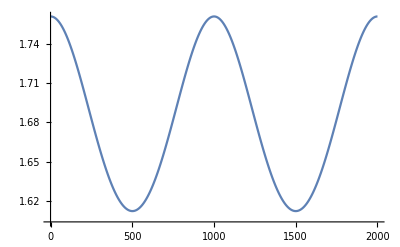

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.